Last modified on: Wednesday, July 11, 2018 at 20:58

Author Info

Faizon Zaman

Matteo Salvarezza

SUNY Oswego

Poster Session Content

Wolfram-Twine Bridge

The goal is to build an Import/Export system between Twine and the Wolfram Language. Twine is browser-based software used to make interactive stories and text-based games. A Twine story or game consists of a network of passages and macros that can change the state of variables or other story elements. Graphs and Associations will be used to represent Twine Stories in the Wolfram Language. The primary goal is importing the Twine Story HTML file into the form of a Wolfram Language Graph and Association, and exporting an Association form to the Twine HTML format.

Add the most representative image of your project here. (We recommend just 1 image, if you add more, we will make a collage of the images.)

-Graphics-

Import support for Twine Stories made using the Harlowe markup language. The importer can generate a Graph and Association from for any html file with the Twine  format. The Twine Link syntax is supported as long as it is not in a macro (commands for changing states of story elements). Using the Association form,  a Twine Summary can be generated to explore the passages via a Clickable Graph. Association Forms  can be exported to the Twine HTML format. A folder is generated in the notebook directory where the story will be stored. These can then be imported into Twine.

The Harlowe markup language has support for macros: commands that can change story elements (appearance, flow, state etc.). Among other types, there are conditional, printing, data and output macros. Some macros include Links to other passages, which I can’t support yet as they are effectively hidden from my parser.  In addition to the macros,  proper passage placement when Importing to the Twine Editor is needed. Going forward, macros should be gradually implemented and the collection of Twine Stories to Import and test on should grow. As errors or unsupported features arise while processing these stories  I will attempt implementations and fixes.

Note: Everything above this bar is your poster.Make sure it fits on a single page. "Preview Poster"

End of School Presentation Content

In addition to the poster content, include other content to present at the 2 minute presentation for end of school. Use the buttons below to add more sections."Add Header""Add Text""Add Code or Image"

Import

-Graphics-

twineImport["~/path/to/file.html"]

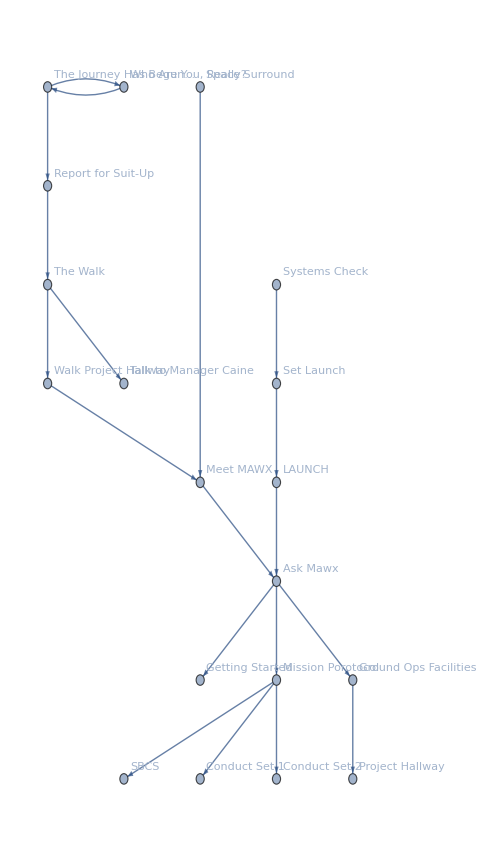

<|"Story Title" → <|"PassageName 1" → "PassageContent 1", ... |>|>

Summary

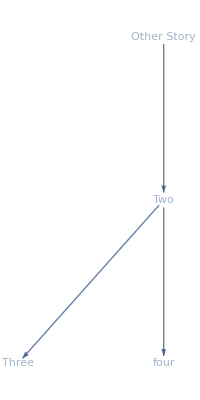
twinePresentationAssoc = <|"Other Story"→<|"Two"→"Go to passage [[Three]] The other node[[four]]","Three"→"Here we are at Passage Three","four"→"Finally at Passage Four."|>|>;

twineSummary[twinePresentationAssoc]
-Graphics-

Output the graph only
twineSummary[twinePresentationAssoc, “Graph”]

Export as Twine HTML to folder called TwineStories in  current notebook directory 
twineSummary[twinePresentationAssoc, “Export”]

Export

Export as Twine HTML to specified folder
twineExport[twinePresentationAssoc, “~/Explicit/Path/For/File”]

Import to Twine

-Graphics--Graphics-

Note: Everything above this bar is in your 2 minute presentation. Make sure it fits on 2 slides. "Preview Presentation"

Detailed Project Notes

#### Main Results in Detail

| IMPORTER |

Import of Twine Stories made using the Harlowe markup language. Harlowe is the default markup language for the Twine Editor  (there are two others: snowman and sugarcube).  On import, a Graph and Association form of the Twine Story are created. Links that only exist as a result of a macro are not supported yet.

| IMPORT HELPER FUNCTIONS |
To keep function definitions lean I’ve created some helper functions ( all except Riccardo’s parser).

| RICCARDO's PARSER | 
The parser takes a string of an html file and generates a nested XMLElement structure from it.

```mathematica
Clear[parseAttrs, parseXML]
$tag =(WordCharacter|"-")..;

parseAttrs[expr_String] := Cases[
StringReplace[
expr,{
k:$tag~~"=\"" ~~ v:Shortest[___] ~~ "\"" :> {k -> v},
k:$tag~~"='" ~~ v:Shortest[___] ~~ "'" :> {k -> v},
k:$tag~~"=" ~~ v:$tag :> {k -> v},
k:$tag :> {k -> ""}
}
],
_Rule,
All
]

parseXML[expr_String] := Quiet[
List @@ StringReplace[
expr,
{"<" ~~ tag:$tag ~~ attrs:Shortest[___] ~~ ">" ~~ body:Shortest[___] ~~ "</" ~~ tag:$tag ~~ ">" :> XMLElement[tag, parseAttrs @ attrs, parseXML@body],
"<" ~~ tag:$tag ~~ attrs:Shortest[___] ~~ "/>" :> XMLElement[tag, parseAttrs @ attrs, {}]
}
],
StringExpression::cond
]
```

| GENERATE EDGES BETWEEN PASSAGES | 
Takes in a passage name and a list of link names found in its respective content and constructs a Directed Edge for each of them.

```mathematica
generateEdges[parentName_, links_]:= Thread[DirectedEdge[parentName, links]]
```

| EXTRACT LINKS FROM PASSAGE CONTENT | 
Takes in passage content and returns all the links found in it. This is used as the second argument to the generateEdges function.

```mathematica
extractLinks[passageContent_]:=
	StringReplace[
		DeleteCases[
			StringCases[passageContent,{
				"[["~~ShortestMatch[linkName___]~~"]]" /; !StringContainsQ[linkName, "->" | "<-" | "|"]:> linkName,
				ShortestMatch["[["~~__~~ShortestMatch["->"~~linkName__]~~"]]"] :> linkName,
				ShortestMatch["[["~~__~~ShortestMatch["|"~~linkName__]~~"]]"] :> linkName,
				ShortestMatch["[["~~ShortestMatch[linkName__ ~~ "<-"]~~__~~"]]"] :> linkName
				}],
		{}], {"&quot;" -> "\"", "&gt;"-> ">", "&lt;" -> "<", "&#39;"-> "'", "&amp;" -> "&", "&nbsp;" -> WhitespaceCharacter}]
```

| EXTRACT STORY DATA FROM IMPORTED STRING | 
Extracts story data from a file at specified path.

```mathematica
extractStoryData[filePath_String]:=Module[{fileAsString, fileSansHeader},
	(* IMPORT FILE AS STRING *)
	fileAsString = Import[filePath, "String"];
	(* GET STORY DATA *)
	fileSansHeader = StringCases[fileAsString, htmlHeader___~~ important:("<tw-storydata"~~ ___ ~~ "</tw-storydata>")~~___ ~~EndOfString:> important];
	(* IF ABOVE RESULT IS A LIST REMOVE BRACES*)
	If[ListQ[fileSansHeader], fileSansHeader /.{fileStringed_} :> fileStringed, fileSansHeader ]
]
```

| GENERATE ASSOCIATION FORM OF STORY | 
Creates an association between passages and content for tooltips. Link syntax is also removed from passage content.

```mathematica
generateStoryAssoc[passages_, root_]:= Module[{passageContentThread},
	
	passageContentThread= 
		AssociationThread[Transpose[passages][[1]] -> StringReplace[Transpose[passages][[2]],
			{
				"[["~~ShortestMatch[linkName___]~~"]]" /; !StringContainsQ[linkName, "->" | "<-" | "|"]:>linkName,
				ShortestMatch["[["~~hiddenName__~~ShortestMatch["->"~~__]~~"]]"] :> hiddenName,
				ShortestMatch["[["~~hiddenName__~~ShortestMatch["|"~~__]~~"]]"] :> hiddenName,
				ShortestMatch["[["~~ShortestMatch[__ ~~ "<-"]~~hiddenName__~~"]]"] :> hiddenName
			}]];
	
	AssociateTo[passageContentThread, root -> "Start Here"];

]
```

| GENREATE GRAPH WITH TOOLTIP VERTICES | 
Generates a graph with tooltips for each vertex.

```mathematica
generateTooltipGraph[rootName_, passages_, assoc_]:=Module[{edges, alledges, g, v},
(* GENERATE PASSAGE EDGES*)
	edges = generateEdges[#[[1]], extractLinks[#[[2]]]]&/@passages;
(* ADD ROOT TO EDGES *)
	alledges = Flatten[{{rootName -> First[passages][[1]]},DeleteCases[edges, {}]}];
(* GENERATE GRAPH FROM ALL EDGES*)
	g = Graph[alledges];
(* ADD TOOLTIPS TO GRAPH VERTICES *)
	v =Table[Tooltip[VertexList[g][[i]], assoc[VertexList[g][[i]]]], {i, 1, Length[VertexList[g]]}];
(* CREATE GRAPH FROM TOOLTIP VETICES AND ALL EDGES*)
	Graph[v, alledges, VertexLabels->"Name",GraphLayout ->{"LayeredDigraphEmbedding", "RootVertex"->rootName}]
]
```

| IMPORT FUNCTION |
Imports a Twine Project and generates a Tooltip Graph and Association from it.

```mathematica
Clear[twineImport]
twineImport[absoluteFilePath_String]:= Module[{file,xmlObject, rootNode,rootNodeName, passages,storyAssociation,completeGraph,assocForm},
	(* EXTRACT STORY DATA FROM HTML FILE *)
	file = extractStoryData[absoluteFilePath];
	(* PARSE EXTRACTED DATA WITH RICCARDO'S PARSER*)
	xmlObject = parseXML[file];
	(* GRAB THE ROOT NODE*)rootNode = Cases[xmlObject, XMLElement["tw-storydata", {Rule["name", _],___}, _]];
     (* GRAB THE ROOT NODE NAME *)rootNodeName =Cases[xmlObject, XMLElement["tw-storydata", {Rule["name", name_],___}, _]:> name]/.{storytitle_}:> storytitle;

(* GRAB ALL PASSAGES *)passages = Cases[rootNode, XMLElement["tw-passagedata", {___,Rule["name", name_],___}, content_]:> {name,content}, {0, Infinity}];
	
(* GENERATE ASSOCIATION FOR TOOLTIP GRAPH GENERATION *)
	storyAssociation = generateStoryAssoc[passages, rootNodeName];
     (* GENERATE TOOLTIP GRAPH*)
	completeGraph = generateTooltipGraph[rootNodeName, passages,storyAssociation];
      (* GENERATE ASSOC FORM*)
	assocForm = Block[{passageContentWithLinks,completeAssociation},
		(*Create Assocation between passage and content*)
		passageContentWithLinks= AssociationThread[Transpose[passages][[1]] -> Transpose[passages][[2]]];
		(*Root Node Association*)
		completeAssociation = <|rootNodeName -> passageContentWithLinks|>];
{completeGraph, assocForm}
]
```

| EXPORTER |
The exporter takes an Association form of a story and exports it as an HTML Fragment to a specified directory that can then be imported into Twine.

```mathematica
Clear[twineExport]
twineExport[associationForm_Association, exportPathToFile_]:=Module[{storyAssoc = associationForm,twGraphVertices,twGraphPoints,sTemplateHeader,assocLength,passageAssoc,passages, stringOfStory},
(* GRAB VERTEX COORDINATES FROM GRAPH *)
twGraphVertices = GraphEmbedding[twineSummary[storyAssoc, "Graph"]];
(* RESCALE COORDINATES FOR PASSAGE POSITIONS *)
twGraphPoints = Reverse[Rescale[Rescale[twGraphVertices],{-1,1}, {0, 250}]];
(* TWINE STORY HEADER *)
sTemplateHeader = StringTemplate["
<tw-storydata name=\"`storyTitle`\" startnode=\"1\" creator=\"Twine\" creator-version=\"2.2.1\" zoom=\"1\" format=\"Harlowe\" format-version=\"2.1.0\" options=\"\" hidden>

  <style role=\"stylesheet\" id=\"twine-user-stylesheet\" type=\"text/twine-css\">
  </style>
  <script role=\"script\" id=\"twine-user-script\" type=\"text/twine-javascript\">
  </script>
"][<|"storyTitle" -> First[Keys[storyAssoc]]|>];
(* PASSAGE ASSOCIATION *)
passageAssoc = First[Values[storyAssoc]];
(* PASSAGE ASSOCIATION LENGTH *)
assocLength = Length[passageAssoc];
(* GENERATE LIST OF PASSAGE DATA*)
passages = Table[
StringTemplate["<tw-passagedata pid=\"`pid`\" 
name=\"`passagename`\" 
tags=\"\"
position=\"`xPos`,`yPos`\"
size=\"100,100\"
>`content`</tw-passagedata>"][<|"pid"-> index,"passagename" -> Keys[passageAssoc][[index]], "content" -> Values[passageAssoc][[index]], "xPos" -> twGraphPoints[[index]][[1]], "yPos" -> twGraphPoints[[index]][[2]] |>], {index, 1,assocLength,1}];
stringOfStory= StringJoin[{sTemplateHeader, passages, "</tw-storydata>"}];
Export[exportPathToFile <>".html",stringOfStory , "HTMLFragment"]
]
```

| SUMMARIZER HELPER FUNCTION |
The cleanPassages  function takes the passage association and removes markdown and link syntax

```mathematica
Clear[cleanPassages]
cleanPassages[passageAssoc_]:= Module[{markdownReplacements,psgContent,psgContentNoLinks,psgContentMarkdownReplaced }, 
(* DEFINE MARKDOWN SYNTAX REPLACEMENTS*)
	markdownReplacements = {"&quot;" -> "\"", "&gt;"-> ">", "&lt;" -> "<", "&#39;"-> "'"};
	(* REPLACE MARKDOWN SYNTAX AND CHARACTER CODES*)psgContent = Table[generateEdges[Flatten[Keys[Values[passageAssoc]]][[index]],Flatten[Values[Values[passageAssoc]]][[index]]], {index, 1, Length[Values[passageAssoc]/.{assc_}:> assc],1}];
	psgContentNoLinks = (psgContent /. DirectedEdge[id_,content_]:> DirectedEdge[id, StringReplace[content, 
		{"[["~~ShortestMatch[linkName___]~~"]]" /; !StringContainsQ[linkName, "->" | "<-" | "|"]:>linkName,
			ShortestMatch["[["~~hiddenName__~~ShortestMatch["->"~~__]~~"]]"] :> hiddenName,
			ShortestMatch["[["~~hiddenName__~~ShortestMatch["|"~~__]~~"]]"] :> hiddenName,
			ShortestMatch["[["~~ShortestMatch[__ ~~ "<-"]~~hiddenName__~~"]]"] :> hiddenName,
			"&quot;" -> "\"", "&gt;"-> ">", "&lt;" -> "<", "&#39;"-> "'", "&nbsp;" -> " ","&amp;" -> "&"
			}
	
	]]);
(* RETURN DIRECTED EDGE CLEANED CONTENT*)
	psgContentMarkdownReplaced = (psgContentNoLinks /. DirectedEdge[id_,content_]:> DirectedEdge[id, StringReplace[content, markdownReplacements]])
]
```

| SUMMARIZER |

The summarizer has three functions; Summary which returns a GraphicsRow containing the Graph with Button vertices and a simple passage display.  Graph which returns the Graph with Button Vertices by itself, and Export which exports the story in HTML format to a folder called TwineStories.

```mathematica
Clear[twineSummary]
twineSummary[userAssoc_, outputForm_:"Summary"]:= Module[{firstEdge, passageEdges,cleanedPassages,buttonList,buttonGraph},
	(* INITIALIZE ACTIVE PASSAGE TO STORY TITLE *)
	Module[{activePassage = First[Keys[userAssoc]], psgKeys = Flatten[Keys[Values[userAssoc]]]},

	(* CREATE THE FIRST EDGE *)
	firstEdge = {First[Keys[userAssoc]]-> Flatten[Keys[Values[userAssoc]]][[1]]};

	(* GENERATE PASSAGE EDGES *)
	passageEdges = Flatten@DeleteCases[Table[generateEdges[psgKeys[[index]], extractLinks[Flatten[Values[Values[userAssoc]]][[index]]]], {index, 1, Length[Values[userAssoc]/.{assc_}:> assc],1}], {}];

	(* CLEAN PASSAGE CONTENT *)
	cleanedPassages = cleanPassages[userAssoc];

	(* GENERATE LIST OF BUTTONS *)
	buttonList = cleanedPassages/. DirectedEdge[name_, content_] :> Button[name, activePassage = content];

	(* REPLACE VERTICES OF THE GRAPH WITH BUTTONS FROM BUTTONLIST *)
	buttonGraph = 
		VertexReplace[
			Graph[Flatten[firstEdge~Join~passageEdges],
			VertexShapeFunction->"Name",
			GraphLayout->{"LayeredDigraphEmbedding","RootVertex"->First[Keys[userAssoc]]}], Table[psgKeys[[i]] -> buttonList[[i]], {i, Length[psgKeys]}]];
(*
	Summary ⇒ {ACTIVEPASSAGE, BUTTONGRAPH} 
	Graph   ⇒ BUTTONGRAPH
	Export  ⇒ EXPORTS TO TwineStories FOLDER IN CURRENT DIRECTORY
*)

	Switch[outputForm,
		"Summary", GraphicsRow[{Dynamic[Framed[activePassage]] , buttonGraph}],
		"Graph", buttonGraph,
		"Export",
			If[DirectoryQ[FileNameJoin[{NotebookDirectory[], "TwineStories"}]],
				Block[{twineFolder},
					twineFolder = FileNameJoin[{NotebookDirectory[], "TwineStories"}];
					twineExport[userAssoc, twineFolder <> "/"<> ToString[First[Keys[userAssoc]]]]
				],
				Block[{twineFolder},
					twineFolder = FileNameJoin[{NotebookDirectory[], "TwineStories"}];
					CreateDirectory[twineFolder];
					twineExport[userAssoc, twineFolder <> "/"<> ToString[First[Keys[userAssoc]]]]
				]
			];
		]
]]
```

| MACRO HANDLING |

Macros are commands that can modify story data and metadata. I’ve thought about a few ways to make that happen. One way, which would be useful is to use GrammarRules, but it is linked to CloudDeploy. What I’ve decided to do is construct a pseudo grammar. 

It takes in an association of the form <| “command” → cmd, “data” → dt |>. 
Some examples:

The set command sets a variable to a value
<| “command” → “set”, “data” → <| “Variable” → “my-var”, “Value” → “my-val” |> |>

The if command returns the value of key “T” if condition is true and the value of key “E” if false.
<|”command”→”if”, “data”→ <|”ConditionExpression”→ condition, “T”→ “True”, “E” → “False” |>|>

The either command returns a random value from the list whose key is “data”.
<|”command”→”either”, “data”→ {a,b,c,d,e,f,g}|>

Here’s the function:

```mathematica
macroGrammar2[macroAssoc_Association]:=Module[{command = macroAssoc["command"], data=macroAssoc["data"]},
Switch[command,
"set",ToExpression[ToString@data["Variable"]<>"="<> ToString@data["Value"]] ,
"if",If[data["ConditionExpression"], data["T"], data["E"]], (*IF*)
"print",Print[data], (*PRINT*)
"either",RandomChoice[data] (*RANDOM Choice*)
]
]
```

#### Code

GitHub Repo

#### Notes

In May I Took a Digital Humanities course where I was introduced to software called Twine. Twine is a browser based app for creating interactive stories and text-based games. A Twine story can be thought of as a website where each webpage is a passage and the story is a network of these passages. In fact, Twine Projects are saved as HTML files.  I thought it might be useful as an algorithm development mind mapping tool, so I suggested it as a project idea.

The project description given to me was to create an Import/Export system between Twine and the Wolfram Language. Where the Wolfram Language representation would be a graph. I’ve implemented both Graph and Association representations.

The browser version of Twine stores intermediate files in local storage which is not accessible. The only file we have access to is the published HTML. The import procedure then is to parse the HTML and follow with conversion to a Graph and Association.

 The main data of a Twine Story has relatively simple structure. It looks like this:
 
 <tw-storydata>
	<tw-passagedata>
 	 	PASSAGE CONTENT
 	 	</tw-passagedata>
 	<tw-passagedata>
 	 	PASSAGE CONTENT
	 	 </tw-passagedata> 
 	 … 
</tw-storydata>
 
Some published Twine Projects have extra HTML, CSS and other data. This data is not needed for my implementation, (nor is it required to import a file into Twine).  All we need is whatever is within the <tw-storydata> tags.

I first tried importing Twine files with the HTML format spec. Though there were problems importing them. Presumably it is because the files are technically invalid HTML.  Since the structure was similar to XML, I tried importing the file as XML, but this did not work either, probably because there was no XML metadata. I then tried XMLObject, which worked to a degree. There was a nesting issue where an extraneous body tag was introduced on import and it separated my content. Riccardo quickly wrote a parser to generate the correct structure. From there I was able to enter the heat of the project. 

With the story data in XML form I could start generating the Graph and Association representation.  I used Cases with XMLElement patterns to extract the story data, story title and passages.

The Graph that comes out of the import function has tooltips on the Vertices so that one can hover over the nodes and see what the content is. It is a quick way to see what the story looks like. To implement this I used an association to help generate the tooltips. This is broken into two functions. One for the association and one for the graph generation. Then I generate the output Association. The Import function outputs a list of the Tooltip Graph and the output Association

Another thing I did was implement an exporter and summarizer. The twineExport function allows one to specify directly  where to save the files via a path string. Initially, the Exported HTML did not work in Twine because I neglected the attributes of tw-storydata and tw-passagedata tags. After I added them the Exports worked. 

The summarizer takes in the association form and can show a button graph with an active passage display, or output just the button graph, or just Export the file. The summarizer exports to the TwineStories folder in the Notebook Directory.

I also started looking into macro implementation. The Macros are commands that can modify story elements. I wanted to implement a Grammar using GrammarRules, but it requires CloudDeploy. What I’ve done instead is define a function called macrogrammar which takes in an association of the form <| “command” →cmd, “data” → d |> and evaluates the command cmd with data d.

#### Conclusions in Detail

I’ve achieved a reasonable foundation for an Import/Export system between Twine and the Wolfram Language. 
One can Import a Valid Twine project and get a graph of all the links ( not in a macro). So at least all passages with “narrative” content are supported. I was able to generate a graph and association form of the story which is a slight extension of the original goal of the project.

I gained  some skills in String Patterning as well. I had some issues isolating all the Link syntaxes, but was able to refine my patterns to isolate the cases I needed to extract.

I now have the framework to build a comprehensive Twine Import/Export system. I can build upon my simple import to include support for macros, and eventually user-scripts. I can build upon my simple export to include support for proper Passage Positioning for the Twine editor. Perhaps, too, I can enhance the Summary function so one can actually play a Twine story or game.

#### Data Sources Links/References

Zip File (Contains the html) | Depths of Sarcasm

#### Future Directions

The Harlowe markup language has support for macros: commands that can change story elements (appearance, flow, state etc.). Among other types, there are conditional, printing, data and output macros. Some macros include Links to other passages, which I can’t support yet as they are effectively hidden from my parser. In addition to this, I need to come up with a good Passage Positioning scheme for Import to Twine, at the moment I’m just scaling the vertices. The other thing to do on the Wolfram Language side is better placement of the Vertex Labels. An option is to use Callouts instead. A nice thing to do as well would be to  format the tooltip text, right now they’re kind of a slog of text. 

The more pressing next step is to gradually implement these macros and continually increase the number of stories I am testing on. For each parsing or macro error in a story, I can implement a fix.

Another possible direction is exporting Wolfram Language based machine generated stories.

Also an Editor workspace in Mathematica for Twine  projects would be useful. As of now one has to write the Association by hand. (of course one can always just use the Twine editor).

Aside from that, the Harlowe markup language is opensource and actively developed — which implies maintenance and updating of functionality as the language changes.

#### Background Info Links/References

Twine Reference

Harlowe Macro Reference

Harlowe Reference

#### Keywords

Provide keywords as items

Twine

Import

Export

Narrative

Explore

Graph

Interactive